```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={k∈Reals,ω∈Complexes, t∈Reals,s∈Reals,R1∈Reals,R2∈Reals,ϵ5∈Reals};
```

# SSH Model

```mathematica
ssh:={{0,t+s*ⅇ^(-ⅈ*k)},{t+s*ⅇ^(ⅈ*k),0}}
```

```mathematica
evalsSSH= Eigenvalues[ssh]//FullSimplify
```

{-ⅇ^(-ⅈ k) √(ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k])),ⅇ^(-ⅈ k) √(ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k]))}

```mathematica
actualEvals={-√(s^2+t^2+2 s t Cos[k]),√(s^2+t^2+2 s t Cos[k])}
```

{-√(s^2+t^2+2 s t Cos[k]),√(s^2+t^2+2 s t Cos[k])}

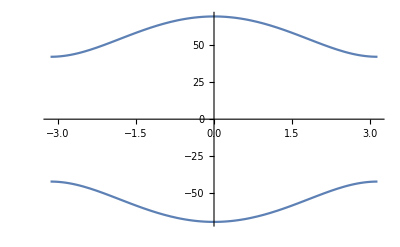

```mathematica
Plot[{actualEvals[[1]],actualEvals[[2]]}/.{s->-13.6,t->-55.7},{k,-π,π}]
```

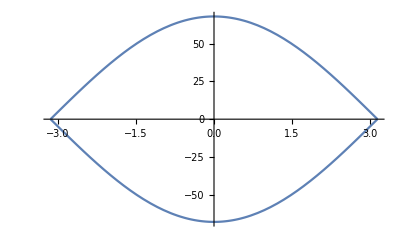

```mathematica
Plot[{actualEvals[[1]],actualEvals[[2]]}/.{s->-34,t->-34},{k,-π,π}]
```

```mathematica
Plot[{actualEvals[[1]],actualEvals[[2]]}/.{s->-55.7,t->-13.6},{k,-π,π}]
```

-Graphics-

```mathematica
evecplus={(t+s*E^(-ⅈ k))/Sqrt[t^2+s^2+2*s*t*Cos[k]],1};
evecminus={(t+s*E^(-ⅈ k))/(-Sqrt[t^2+s^2+2*s*t*Cos[k]]),1};
```

```mathematica
Aplus=ⅈ (Conjugate[evecplus].D[evecplus,k])//ComplexExpand//FullSimplify
```

(s (s+t Cos[k]))/(s^2+t^2+2 s t Cos[k])

```mathematica
Aminus=ⅈ (Conjugate[evecminus].D[evecminus,k])//ComplexExpand//FullSimplify
```

(s (s+t Cos[k]))/(s^2+t^2+2 s t Cos[k])

```mathematica
phi=ArcTan[s Sin[k]/(t+s Cos[k])];
phiplus={Exp[-ⅈ phi],1};
phiminus={-Exp[-ⅈ phi],1};
braphi=Conjugate[phiplus];
ketphi=D[phiplus,k];
```

```mathematica
AplusCheck=ⅈ (Conjugate[phiplus].D[phiplus,k])//ComplexExpand//FullSimplify
AminusCheck=ⅈ (Conjugate[phiminus].D[phiminus,k])//ComplexExpand//FullSimplify
```

(s (s+t Cos[k]))/(s^2+t^2+2 s t Cos[k])

(s (s+t Cos[k]))/(s^2+t^2+2 s t Cos[k])

```mathematica
zakplus=1/π Integrate[Aplus,{k,-π,π}]
```

1+Sign[s^2-t^2]

```mathematica
zakminus=1/π Integrate[Aminus,{k,-π,π}]
```

1+Sign[s^2-t^2]

```mathematica
deltaZak=zakplus-zakminus//FullSimplify
```

0

# Top. Subspace Paper

```mathematica
H={{0,t+s*ⅇ^(-ⅈ*k),0,0,R1},{t+s*ⅇ^(ⅈ*k),0,0,0,0},{0,0,0,t+s*ⅇ^(-ⅈ*k),R2},{0,0,t+s*ⅇ^(ⅈ*k),0,0},{R1,0,R2,0,ϵ5}};
```

```mathematica
Eigenvalues[H]//ComplexExpand//FullSimplify
```

{-ⅇ^(-ⅈ k+1/2 ⅈ Arg[ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k])]) √(s^2+t^2+2 s t Cos[k]),ⅇ^(-ⅈ k+1/2 ⅈ Arg[ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k])]) √(s^2+t^2+2 s t Cos[k]),ⅇ^(-ⅈ k) Root[ⅇ^(3 ⅈ k) s^2 ϵ5+ⅇ^(2 ⅈ k) s t ϵ5+ⅇ^(4 ⅈ k) s t ϵ5+ⅇ^(3 ⅈ k) t^2 ϵ5+(-ⅇ^(2 ⅈ k) R1^2-ⅇ^(2 ⅈ k) R2^2-ⅇ^(2 ⅈ k) s^2-ⅇ^(ⅈ k) s t-ⅇ^(3 ⅈ k) s t-ⅇ^(2 ⅈ k) t^2) #1-ⅇ^(ⅈ k) ϵ5 #1^2+#1^3&,1],ⅇ^(-ⅈ k) Root[ⅇ^(3 ⅈ k) s^2 ϵ5+ⅇ^(2 ⅈ k) s t ϵ5+ⅇ^(4 ⅈ k) s t ϵ5+ⅇ^(3 ⅈ k) t^2 ϵ5+(-ⅇ^(2 ⅈ k) R1^2-ⅇ^(2 ⅈ k) R2^2-ⅇ^(2 ⅈ k) s^2-ⅇ^(ⅈ k) s t-ⅇ^(3 ⅈ k) s t-ⅇ^(2 ⅈ k) t^2) #1-ⅇ^(ⅈ k) ϵ5 #1^2+#1^3&,2],ⅇ^(-ⅈ k) Root[ⅇ^(3 ⅈ k) s^2 ϵ5+ⅇ^(2 ⅈ k) s t ϵ5+ⅇ^(4 ⅈ k) s t ϵ5+ⅇ^(3 ⅈ k) t^2 ϵ5+(-ⅇ^(2 ⅈ k) R1^2-ⅇ^(2 ⅈ k) R2^2-ⅇ^(2 ⅈ k) s^2-ⅇ^(ⅈ k) s t-ⅇ^(3 ⅈ k) s t-ⅇ^(2 ⅈ k) t^2) #1-ⅇ^(ⅈ k) ϵ5 #1^2+#1^3&,3]}

```mathematica
Hbd={{0,t+s*ⅇ^(-ⅈ*k),0,0,r1},{t+s*ⅇ^(ⅈ*k),0,0,0,0},{0,0,0,t+s*ⅇ^(-ⅈ*k),Sqrt[R1^2+R2^2]},{0,0,t+s*ⅇ^(ⅈ*k),0,0},{0,0,Sqrt[R1^2+R2^2],0,ϵ5}};
```

```mathematica
Eigenvalues[Hbd]//FullSimplify
```

{-ⅇ^(-ⅈ k) √(ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k])),ⅇ^(-ⅈ k) √(ⅇ^(2 ⅈ k) (s^2+t^2+2 s t Cos[k])),ⅇ^(-ⅈ k) Root[ⅇ^(3 ⅈ k) s^2 ϵ5+ⅇ^(2 ⅈ k) s t ϵ5+ⅇ^(4 ⅈ k) s t ϵ5+ⅇ^(3 ⅈ k) t^2 ϵ5+(-ⅇ^(2 ⅈ k) R1^2-ⅇ^(2 ⅈ k) R2^2-ⅇ^(2 ⅈ k) s^2-ⅇ^(ⅈ k) s t-ⅇ^(3 ⅈ k) s t-ⅇ^(2 ⅈ k) t^2) #1-ⅇ^(ⅈ k) ϵ5 #1^2+#1^3&,1],ⅇ^(-ⅈ k) Root[ⅇ^(3 ⅈ k) s^2 ϵ5+ⅇ^(2 ⅈ k) s t ϵ5+ⅇ^(4 ⅈ k) s t ϵ5+ⅇ^(3 ⅈ k) t^2 ϵ5+(-ⅇ^(2 ⅈ k) R1^2-ⅇ^(2 ⅈ k) R2^2-ⅇ^(2 ⅈ k) s^2-ⅇ^(ⅈ k) s t-ⅇ^(3 ⅈ k) s t-ⅇ^(2 ⅈ k) t^2) #1-ⅇ^(ⅈ k) ϵ5 #1^2+#1^3&,2],ⅇ^(-ⅈ k) Root[ⅇ^(3 ⅈ k) s^2 ϵ5+ⅇ^(2 ⅈ k) s t ϵ5+ⅇ^(4 ⅈ k) s t ϵ5+ⅇ^(3 ⅈ k) t^2 ϵ5+(-ⅇ^(2 ⅈ k) R1^2-ⅇ^(2 ⅈ k) R2^2-ⅇ^(2 ⅈ k) s^2-ⅇ^(ⅈ k) s t-ⅇ^(3 ⅈ k) s t-ⅇ^(2 ⅈ k) t^2) #1-ⅇ^(ⅈ k) ϵ5 #1^2+#1^3&,3]}